Block Encoding |

Block Encodingpaclet:QuantumMob/Q3/tutorial/BlockEncoding#1159336212 | Examplespaclet:QuantumMob/Q3/tutorial/BlockEncoding#4935158
The GSLW Conventionpaclet:QuantumMob/Q3/tutorial/BlockEncoding#618934295 |

Block encoding is a method to get a quantum computer accessible to the information in a matrix M. Typically, the resulting bigger embedding matrix is denoted by U_M and has the block form

U_M:=(M | *
* | *) ,

where * indicates the corresponding block is irrelevant.

BlockEncodingpaclet:QuantumMob/Q3/ref/BlockEncodingQuantumMob Package Symbol | Implements a block encoding of a matrix
UniformlyControlledGatepaclet:QuantumMob/Q3/ref/UniformlyControlledGateQuantumMob Package Symbol | Uniformly controlled unitary gates

Q3 functions related to an implementation of block encoding.

Make sure that the Q3: Symbolic Quantum Simulation package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to refer to a quantum register of qubits. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Block Encoding

Let M be a N×N (with N:=2^n) complex matrix, which is not unitary in general. Suppose that M has the singular-value decomposition M=VΛ W^†, where V and W are unitary matrices and Λ:=diagonal(λ_1,λ_2,…,λ_N)≥0 is the diagonal matrix of singular values. We assume that the singular values are all less than 1; 0≤λ_k≤1. Note that this is not a restriction since one can always rescale the matrix by a constant factor.

In Q3, the block encoding is implemented as

M↦U_M:=(V | 0
0 | V)(Λ | √(1-Λ^2)
√(1-Λ^2) | -Λ)(W^† | 0
0 | W^†) .

### Quantum Circuit Model

For a quantum circuit model of this implementation, we introduce a rotated basis state

θ:=R_y(θ)0≐(cos(θ/2)
sin(θ/2))

and the reflection in the line along the vector θ (see also Figure 2 for a geometric interpretation)

Ω_y(cosθ):=2θθ-1=R_y(θ)ZR_y^†(θ)≐(cosθ | sinθ
sinθ | -cosθ).

Now, note that

(λ | √(1-λ^2)
√(1-λ^2) | -λ)≐Ω_y(λ)=Ω_y(cosθ)

with cosθ:=λ (i.e., sinθ=√(1-λ^2)). Therefore, the block encoding U_M can be rewritten as

U_M=(I⊗V)(Σ_k Ω_y(λ_k)⊗kk)(I⊗W^†),

where cos θ_k:=λ_k and {k:k=0,1,…,2^n-1} is the computational basis of the system register. In particular, the expression Σ_k Ω_y(λ_k)⊗kk in the middle is nothing but the uniformly-controlled unitary gate operating Ω_y(λ_k) conditioned on the state k of the system register.

Putting all together, the block encoding U_M may be described by the quantum circuit in Figure 1.

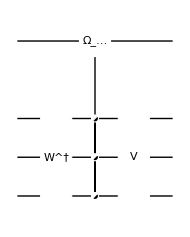
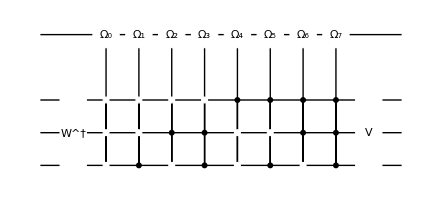
=-Graphics-=-Graphics-

Figure 1. Equivalent quantum circuits representing the block encoding of matrix M that has singular value decomposition M=VΛ W^† with Λ:=diag(λ_1,λ_2,,…,λ_n). Here, Ω_k is a short-hand notation for Ω_k:=Ω_y(λ_k)=Ω_y(cosθ_k) with cos(θ_k):=λ_k.

As one can see in Figure 1, the computational cost of block encoding is exponentially high in general.

### Remark: Alternative Block Encoding

Another common implementation of block encoding is through the mapping [see, e.g., Lin (2022)]

M↦(V | 0
0 | I)(Λ | √(1-Λ^2)
√(1-Λ^2) | -Λ)(W^† | 0
0 | I) .

Q3 does not consider this because (V | 0
0 | I) and (W^† | 0
0 | I) correspond to controlled-unitary gates. When V and W are large, the actual implementation of those controlled-unitary gates may be computationally expensive.

### Geometric View: Relation to the Grover Rotation

The reflection Ω_y(cosθ) in the line along the vector θ can be converted to the rotation around the y-axis by angle 2θ by multiplying the Pauli Z operator. In other words, it is useful to define a Grover-like rotation around the y-axis by

G_y(λ):=Ω_y(cosθ)Z=R_y(θ)ZR_y^†(θ)Z=R_y(θ)R_y(θ)=R_y(2θ)≐(cosθ | -sinθ
sinθ | cosθ) .

This relation can also be understood with a geometrical view as shown in Figure 2. The Grover rotation in quantum search algorithm has also a similar geometric interpretation.

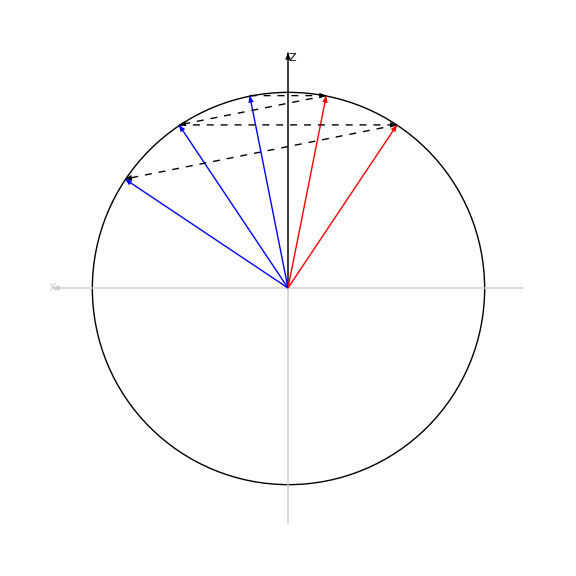

Figure 2. A geometric view of the effects of the reflection Z in the line along the computational basis vector 0 (from blue to red arrows) and the reflection Ω_y(cosθ) in the line along the rotated basis vector θ:=R_y(θ)0 (from red to blue arrows). Combining  Ω_y(cosθ) with Z gives rise to the Grover rotation (from blue to blue arrows). Shown is the zx-plane in the Bloch space with the z-axis in the vertical direction and the y-axis pointing out of the screen.

The GSLW Convention

In GSLW (Gilyén, Su, Low and Wiebe, 2019),  the block encoding is implemented as

M↦U_M:=(V | 0
0 | V)(Λ | ⅈ √(1-Λ^2)
ⅈ √(1-Λ^2) | Λ)(W^† | 0
0 | W^†) .

### Quantum Circuit Model

For a quantum circuit model of this implementation, we introduce a Grover-like rotation around the x-axis,

G_x(λ):=(λ | ⅈ √(1-λ^2)
ⅈ √(1-λ^2) | λ).

It turns out that with cosθ:=λ (i.e., sinθ=√(1-λ^2)),
	G_x(λ)=G_x(cosθ)=R_x^†(2θ)≐(cosθ | ⅈsinθ
ⅈsinθ | cosθ) .

In passing, note  that the Grover-like rotation around the x-axis and the one around y-axis seen before are related to each other by

G_x(λ)=ⅇ^(-ⅈZπ/4)G_y(λ)ⅇ^(ⅈZπ/4) .

The GSLW form of block encoding U_M can be rewritten as

U_M=(I⊗V)(Σ_k G_x(λ_k)⊗kk)(I⊗W^†).

where again {k:k=0,1,…,2^n-1} is the computational basis of the system register. Clearly, the expression Σ_k G_x(λ_k)⊗kk in the middle is nothing but the uniformly-controlled unitary gate operating G_x(λ_k)conditioned on the state k of the system register.

Putting all together, the block encoding U_M may be described by the quantum circuit in Figure 3.

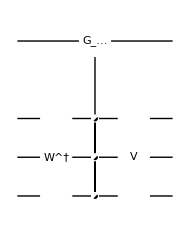
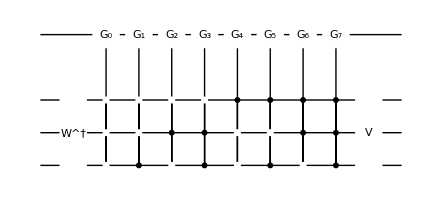
=-Graphics-=-Graphics-

Figure 3. Equivalent quantum circuits representing the GSLW block encoding of matrix M that has singular value decomposition M=VΛ W^† with Λ:=diag(λ_1,λ_2,,…,λ_n). Here, G_k is a short-hand notation for G_k:=G_x(λ_k)=G_x(cosθ_k) with cos(θ_k):=λ_k.

### Geometric View: Relation to the Grover Rotation

The GSLW form of block encoding also allows a similar geometric interpretation as the standard form in the above. To see this, let us introduce the rotated basis vector

x:-θ:=R_x^†(θ)0≐(cos(θ/2)
ⅈsin(θ/2))

and the reflection in the line along the vector x:-θ (see also Figure 4 for a geometric interpretation)

Ω_x(cosθ):=2x:-θx:-θ-1=R_x(-θ)ZR_x^†(-θ)≐(cosθ | -ⅈsinθ
ⅈsinθ | -cosθ).

Now, note that

G_x(λ)≐(λ | ⅈ √(1-λ^2)
ⅈ √(1-λ^2) | λ)=Ω_x(λ)Z=Ω_x(cosθ)Z=R_x^†(2θ).

In other words, combined with the Pauli Z operator, the reflection Ω_x(cosθ) in the line along the vector x:-θ gives rise to the rotation around the x-axis by angle 2θ

Ω_x(cosθ)Z=R_x(-θ)ZR_x^†(-θ)Z=R_x(-θ)R_x(-θ)=R_x(-2θ)≐(cosθ | ⅈsinθ
ⅈ sinθ | cosθ) .

This relation becomes even clearer with a geometrical view as shown in Figure 4.

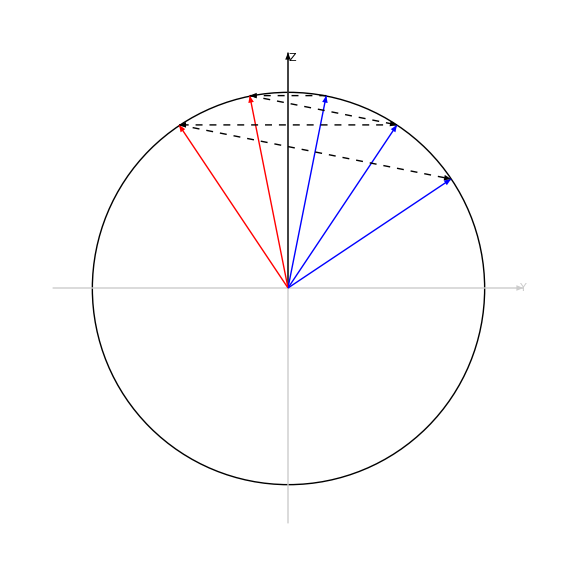

Figure 4. A geometric view of the effects of the reflection Z in the line along the computational basis vector 0 (from blue to red arrows) and the reflection Ω_x(cosθ) in the line along the rotated basis vector x:-θ:=R_x^†(θ)0 (from red to blue arrows). The combining Ω_x(cosθ) with Z gives rise to the Grover rotation (from blue to blue arrows). Shown is the yz-plane in the Bloch space with the z-axis in the vertical direction and the x-axis pointing out of the screen.

Moreover, recalling the relation the Grover-like rotations around x- and y-axis

G_x(λ)=ⅇ^(-ⅈZπ/4)G_y(λ)ⅇ^(ⅈZπ/4) ,

we immediately see a similar relation between the reflections

Ω_x(λ)=ⅇ^(-ⅈZπ/4)Ω_y(λ)ⅇ^(ⅈZπ/4) .

Examples

Make sure that the Q3: Symbolic Quantum Simulation package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

We will consider two registers and refer to them by these symbols, respectively.

```mathematica
Let[Qubit,S,A]
```

Consider a system register of n qubits.

```mathematica
$n=3;
$N=Power[2,$n];
SS=S[Range@$n,$]
```

{S_(,,1),S_(,,2),S_(,,3)}

We are going to block-encode a matrix representing a linear operator acting on the system register by using an ancilla register of m qubits.

```mathematica
$m=2;
AA=A[Range@$m,$]
```

{A_(,,1),A_(,,2)}

For later use, define a variable representing the total register.

```mathematica
AS=Join[AA,SS];
```

Take a matrix representing an operator on the system register.

```mathematica
in=(ThePauli[{2,3,1}]+(I/2)*ThePauli[{3,2,2}])/4;
in//MatrixForm
```

(0 | 0 | 0 | -ⅈ/8 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | ⅈ/8 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
-ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0
0 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
ⅈ/4 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0
0 | 0 | 0 | -ⅈ/4 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | -ⅈ/4 | 0 | ⅈ/8 | 0 | 0 | 0)

Block-encode the matrix using the ancilla register.

```mathematica
enc=BlockEncoding[in,SS,AA]
```

BlockEncoding[…]

Display the block encoding in a quantum circuit.

```mathematica
qc=QuantumCircuit[enc]
```

-Graphics-

Convert the block-encoding into the matrix representation, and check the block to make sure the input matrix has been properly embedded.

```mathematica
mat=Matrix[enc];
mat[[;;$N,;;$N]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ/8 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | ⅈ/8 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
-ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0
0 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
ⅈ/4 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0
0 | 0 | 0 | -ⅈ/4 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | -ⅈ/4 | 0 | ⅈ/8 | 0 | 0 | 0)

For a matrix M with singular-value decomposition M=VΛ W^†, Q3 implements the quantum singular-value transform as
	M↦(V | 0
0 | V)(Λ | √(1-Λ^2)
√(1-Λ^2) | -Λ)(W^† | 0
0 | W^†),
where V and W are unitary matrices and Λ:=diagonal(λ_1,λ_2,…)≥0 are singular values. This implementation is described as below. Here, we have used a short-hand notation Ω_k:=Ω_θ_k with cos(θ_k):=λ_k and 
	Ω_θ≐(cosθ | sinθ
sinθ | -cosθ).

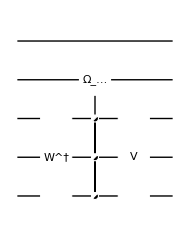

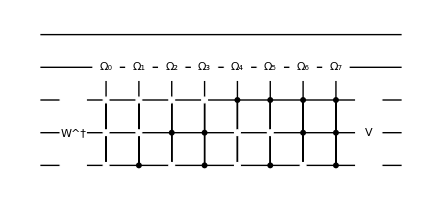

```mathematica
new=Expand[enc]
alt=Expand[new]
```

Check that these equivalent quantum circuits indeed reproduce the same matrix.

```mathematica
mint=Matrix[new,AS];
mint[[;;$N,;;$N]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ/8 | 0 | -ⅈ/4 | 0 | 0
0 | 0 | ⅈ/8 | 0 | -ⅈ/4 | 0 | 0 | 0
0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
-ⅈ/8 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0
0 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
ⅈ/4 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0
0 | 0 | 0 | -ⅈ/4 | 0 | -ⅈ/8 | 0 | 0
0 | 0 | -ⅈ/4 | 0 | ⅈ/8 | 0 | 0 | 0)

```mathematica
mint-mat//Chop//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Calculate the operator expression of the block-encoding on the total register.

```mathematica
EchoTiming[expr=Elaborate[enc]//Elaborate]
```

4.53387

1/16 (3 √7+√55) A_(,,2)^(,,X)S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,X)-1/16 ⅈ (3 √7-√55) A_(,,2)^(,,X)S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Y)+1/4 A_(,,2)^(,,Z)S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,X)+1/8 ⅈ A_(,,2)^(,,Z)S_(,,1)^(,,Z)S_(,,2)^(,,Y)S_(,,3)^(,,Y)

```mathematica
del=Matrix[alt,AS]-mat;
del//SimplifyThrough//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪A. Gilyen, Y. Su, G. Hao, and N. Wiebe (2019)https://doi.org/10.1145/3313276.3316366, Proceedings of the 51st Annual ACM SIGACT Symposium on Theory of Computing, "Quantum singular value transformation and beyond: exponential improvements for quantum matrix arithmetics."
▪L. Lin (2022)https://arxiv.org/abs/2201.08309, arXiv:2201.08309, "Lecture Notes on Quantum Algorithms for Scientific Computation."
▪J. M. Martyn, Z. M. Rossi, A. K. Tan, I. L. Chuan (2021)https://doi.org/10.1103%2Fprxquantum.2.040203, PRX Quantum 2, 4 040203, "Grand Unification of Quantum Algorithms."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).